```mathematica
Quit
```

```mathematica
Integrate[Exp[10/1(1/r-1)] r^2,{r,1,∞}]
```

Integrate::idiv: Integral of ⅇ^10\ (-1 + 1/r)\ r^2 does not converge on {1, ∞}.

∫_1^∞ ⅇ^(10 (-1+1/r)) r^2ⅆr

```mathematica
Clear[h]
```

```mathematica
Assuming[rr > 1,Integrate[Exp[1/h(1/r-1)] r^2,{r,1,rr}]]
```

1/(6 h^3)ⅇ^(-1/h) (-ⅇ^(1/h) h (1+h+2 h^2)+ⅇ^(1/(h rr)) h rr (1+h rr (1+2 h rr))+ExpIntegralEi[1/h]-ExpIntegralEi[1/(h rr)])

```mathematica
(ⅇ^(-1/h) (ⅇ^(1/(h r)) h r (1+h r+2 h^2 r^2)-ExpIntegralEi[1/(h r)]))/(6 h^3)/. r-> 1
```

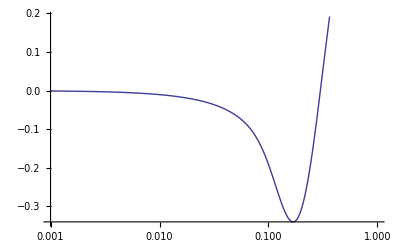

```mathematica
LogLinearPlot[(ⅇ^(-1/h) (ⅇ^(1/h) h (1+h+2 h^2)-ExpIntegralEi[1/h]))/(6 h^3),{h,.001,1}]
```

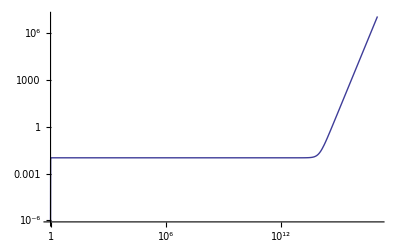

```mathematica
h = .01;
LogLogPlot[1/(6 h^3)ⅇ^(-1/h) (-ⅇ^(1/h) h (1+h+2 h^2)+ⅇ^(1/(h rr)) h rr (1+h rr (1+2 h rr))+ExpIntegralEi[1/h]-ExpIntegralEi[1/(h rr)]),{rr,1,10^17},PlotRange->All]
```

```mathematica
Integrate
```